```mathematica
fitO := o + (b-c)*y + b*B;
fitY := b*o + y + (b-c)*B;
fitB := o*(b-c) + b*y + B;

fitmedio := fitO * o + fitY * y + fitB * B;

dodt := o * (fitO - fitmedio);
dydt := y * (fitY - fitmedio);
dbdt := B * (fitB - fitmedio);

equilibrio = Solve[{dodt == 0 && dydt == 0 && dbdt == 0, o + y + B ==1}, {o, y, B}]
```

{{o→0,y→1,B→0},{o→(-1+b-c)/(-2+2 b-c),y→(-1+b)/(-2+2 b-c),B→0},{o→0,y→(-1+b-c)/(-2+2 b-c),B→(-1+b)/(-2+2 b-c)},{o→0,y→0,B→1},{o→1/3,y→1/3,B→1/3},{o→1,y→0,B→0},{o→(-1+b)/(-2+2 b-c),y→0,B→(-1+b-c)/(-2+2 b-c)}}

```mathematica
jacobiana=FullSimplify[D[{dodt,dydt,dbdt},{{o,y,B}}]];
MatrixForm[jacobiana]
```

(-B^2+2 o+2 B c o-3 o^2+c (-1+B+2 o) y-y^2+b (B-4 B o+y-2 B y-4 o y) | o (b (1-2 B-2 o)+c (-1+B+o)-2 y) | o (-2 B+b (1-2 o-2 y)+c (o+y))
y (-2 o+b (1-2 B-2 y)+c (B+y)) | -B^2-o^2+2 y+2 c o y-3 y^2+B c (-1+o+2 y)+b (B+o-2 B o-4 (B+o) y) | y (-2 B+b (1-2 o-2 y)+c (-1+o+y))
B (-2 o+b (1-2 B-2 y)+c (-1+B+y)) | B (b (1-2 B-2 o)+c (B+o)-2 y) | -3 B^2-o (c+o)+c o y-y^2+b (o+y-2 o y)+2 B (1-2 b (o+y)+c (o+y)))

```mathematica
mat1=jacobiana/. {o->0,y->1,B->0};
autovalores1=Eigenvalues[mat1]
Resolve[Exists[{b,c},b>=1&&c>=0&&-1+b-c<=0 && Max[Re[autovalores1]]<0]]
```

{-1,-1+b,-1+b-c}

False

```mathematica
mat2=jacobiana/. {o->1,y->0,B->0};
autovalores2=Eigenvalues[mat2]
Resolve[Exists[{b,c},b>=1&&c>=0&&-1+b-c<=0 && Max[Re[autovalores2]]<0]]
```

{-1,-1+b,-1+b-c}

False

```mathematica
mat3=jacobiana/. {o->0,y->0,B->1};
autovalores3=Eigenvalues[mat3]
Resolve[Exists[{b,c},b>=1&&c>=0&&-1+b-c<=0 && Max[Re[autovalores3]]<0]]
```

{-1,-1+b,-1+b-c}

False

```mathematica
mat4=jacobiana/. {o->1/3,y->1/3,B->1/3};
autovalores4=Eigenvalues[mat4]
Resolve[Exists[{b,c},b>=1&&c>=0&&-1+b-c<=0 && Max[Re[autovalores4]]<0]]
Reduce[b>=1&&c>=0&&-1+b-c<=0&&Max[Re[autovalores4]]<0,{b,c},Reals]
```

{1/3 (-1-2 b+c),1/6 (2-2 b+c+ⅈ √3 c),1/6 (2-2 b+c-ⅈ √3 c)}

True

b>1&&-1+b≤c<-2+2 b

b>1&&-1+b≤c<-2+2 b

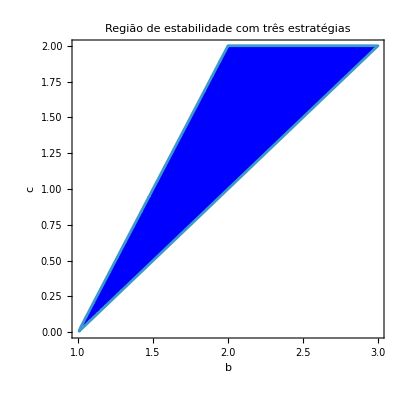

```mathematica
region4 = Reduce[b>=1&&c>=0&&-1+b-c<=0&&Max[Re[autovalores4]]<0,{b,c},Reals]
RegionPlot[region4&&Max[Re[autovalores4]]<0,
{b,1,3},{c,0,2},
PlotStyle->{Blue,Opacity[1]},
PlotLegends->"Expressions",
FrameLabel->{"b","c"},
PlotLabel->"Região de estabilidade com três estratégias"]
```

```mathematica
mat5=jacobiana/. {o->(-1+b-c)/(-2+2 b-c),y->(-1+b)/(-2+2 b-c),B->0};
autovalores5=Eigenvalues[mat5]
Resolve[Exists[{b,c},b>=1&&c>=0&&-1+b-c<=0 && 0<= (-1+b-c)/(-2+2 b-c) <=1 && 0<=(-1+b)/(-2+2 b-c)<=1 && Max[Re[autovalores5]]<0]]
```

{(1-b^2+b c)/(-2+2 b-c),(-1+2 b-b^2-c+b c)/(-2+2 b-c),(1-2 b+b^2+c-b c+c^2)/(-2+2 b-c)}

False

```mathematica
region5 = Reduce[b>=1&&c>=0&&-1+b-c<=0&&Max[Re[autovalores5]]<0,{b,c},Reals]
```

b>1&&c>-2+2 b

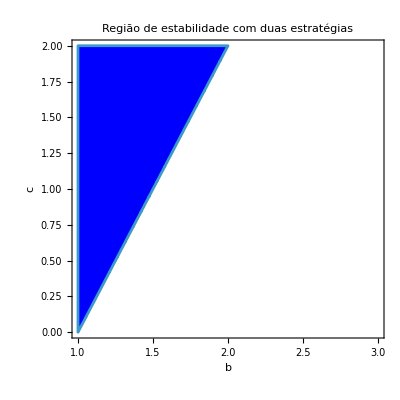

```mathematica
RegionPlot[region5&&Max[Re[autovalores5]]<0,
{b,1,3},{c,0,2},
PlotStyle->{Blue,Opacity[1]},
PlotLegends->"Expressions",
FrameLabel->{"b","c"},
PlotLabel->"Região de estabilidade com duas estratégias"]
```

```mathematica
mat6=jacobiana/. {o->0,y->(-1+b-c)/(-2+2 b-c),B->(-1+b)/(-2+2 b-c)};
autovalores6=Eigenvalues[mat6]
Resolve[Exists[{b,c},b>=1&&c>=0&&-1+b-c<=0 &&0<=(-1+b-c)/(-2+2 b-c)<=1 && 0<= (-1+b)/(-2+2 b-c)<=1 && Max[Re[autovalores6]]<0]]
region6 = Reduce[b>=1&&c>=0&&-1+b-c<=0&&Max[Re[autovalores6]]<0,{b,c},Reals]
RegionPlot[region6 &&Max[Re[autovalores6]]<0,
{b,1,3},{c,0,2},
PlotStyle->{Blue,Opacity[1]},
PlotLegends->"Expressions",
FrameLabel->{"b","c"},
PlotLabel->"Região de estabilidade com duas estratégias"]
```

{(1-b^2+b c)/(-2+2 b-c),(-1+2 b-b^2-c+b c)/(-2+2 b-c),(1-2 b+b^2+c-b c+c^2)/(-2+2 b-c)}

False

b>1&&c>-2+2 b

-Graphics-

```mathematica
mat7=jacobiana/. {o->(-1+b)/(-2+2 b-c),y->0,B->(-1+b-c)/(-2+2 b-c)};
autovalores7=Eigenvalues[mat7]
Resolve[Exists[{b,c},b>=1&&c>=0&&-1+b-c<=0 && 0<=(-1+b-c)/(-2+2 b-c)<=1 && 0<= (-1+b)/(-2+2 b-c)<=1 && Max[Re[autovalores7]]<0]]
region7 = Reduce[b>=1&&c>=0&&-1+b-c<=0&&Max[Re[autovalores7]]<0,{b,c},Reals]
RegionPlot[region7 &&Max[Re[autovalores7]]<0,
{b,1,3},{c,0,2},
PlotStyle->{Blue,Opacity[1]},
PlotLegends->"Expressions",
FrameLabel->{"b","c"},
PlotLabel->"Região de estabilidade com duas estratégias"]
```

{(1-b^2+b c)/(-2+2 b-c),(-1+2 b-b^2-c+b c)/(-2+2 b-c),(1-2 b+b^2+c-b c+c^2)/(-2+2 b-c)}

False

b>1&&c>-2+2 b

-Graphics-

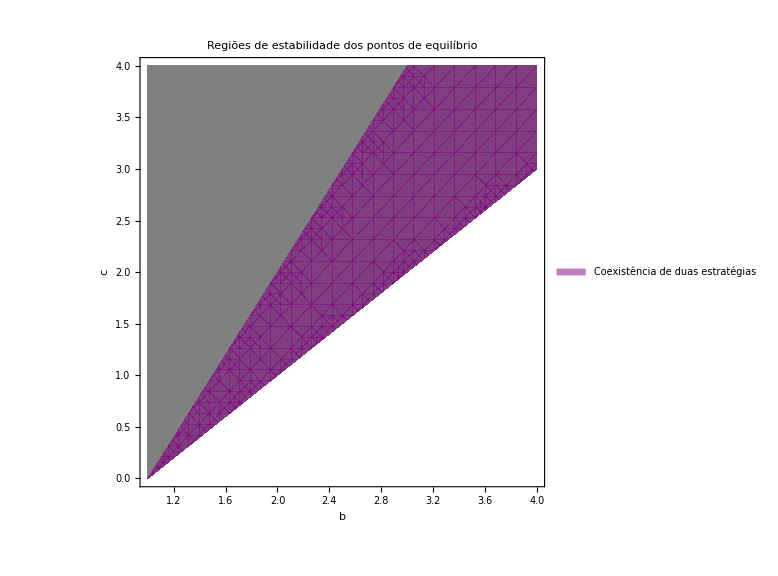

```mathematica
(*Ponto 3 estratégias*)
plotMix=RegionPlot[b>=1&&c>=0&&-1+b-c<=0 &&Max[Re[autovalores4]]<0,
{b,1,4},{c,0,4},
PlotStyle->{Purple,Opacity[0.5]},
BoundaryStyle->None,
PlotLegends->Placed[{"Coexistência de duas estratégias"},Below]];

(*Ponto com duas estratégias*)
plotOY=RegionPlot[b>=1&&c>=0&&-1+b-c<=0&& 0<=(-1+b-c)/(-2+2 b-c)<=1&&0<=(-1+b)/(-2+2 b-c)<=1&&Max[Re[autovalores5]]<0,
{b,1,4},{c,0,4},
PlotStyle->{Orange,Opacity[0.5]},
BoundaryStyle->None];

plotGray=RegionPlot[b>=1&&c>=0&&-1+b-c<=0,
{b,1,4},{c,0,4},
PlotStyle->{Gray,Opacity[1]},
BoundaryStyle->None,
RegionFunction->Function[{b,c,x,y},!(Max[Re[autovalores4]]<0||Max[Re[autovalores5]]<0)],
PlotLegends->None];

(*sobrepondo todos*)
Show[plotGray,plotMix,plotOY, FrameLabel->{"b","c"},PlotLabel->"Regiões de estabilidade dos pontos de equilíbrio",ImageSize->Large]
```